## 1D Fourier Quantum Process Tomography

### Experimental parameters

```mathematica
pixelsize=5.2*10^-6(*in meters*);
Λ=2.5*10^-3(*spatial period, in meters*);
```

```mathematica
pixels=Round[Λ/pixelsize](*how many pixels in a period*)
```

481

### Algorithm parameters

```mathematica
offsets=64;
globalphase=Subdivide[0,2N[Pi],offsets-1](*global offsets for reconstructed phases*);
trials=100(*how many independent executions of the GS algorithm*);
iterations=1000(*how many iterations within a single execution*);
```

## Import experimental data

```mathematica
SetDirectory[NotebookDirectory[]<>"\\Data\\1D"]
```

C:\Users\franc\Desktop\postdoc\research\QPT_GS\github\Data\1D

```mathematica
HHnear=Import["HH_near.txt","List"];
HHfar=Import["HH_far.txt","List"];
```

```mathematica
DDnear=Import["DD_near.txt","List"];
DDfar=Import["DD_far.txt","List"];
```

```mathematica
LLnear=Import["LL_near.txt","List"];
LLfar=Import["LL_far.txt","List"];
```

```mathematica
probtot=Import["far_total.txt","List"];
```

## HH

### Phase retrieval

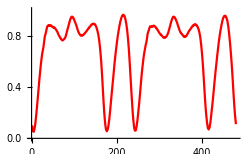
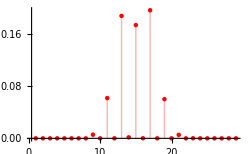

```mathematica
{ListPlot[HHnear,PlotStyle->Red,Joined->True,PlotRange->{0,1},ImageSize->250],ListPlot[HHfar,PlotRange->All,PlotStyle->Red,Joined->False,Filling->Axis,ImageSize->250]}
```

```mathematica
HHfar=ArrayPad[HHfar,(pixels-Length[HHfar])/2](*array-padding needed for implementing the FFT*);
```

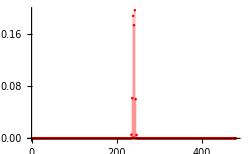
{-Graphics-,-Graphics-}

```mathematica
{ListPlot[HHnear,PlotStyle->Red,Joined->True,PlotRange->{0,1},ImageSize->250],ListPlot[HHfar,PlotRange->All,PlotStyle->Red,Joined->False,Filling->Axis,ImageSize->250]}
```

```mathematica
Dimensions[HHnear]==Dimensions[HHfar]
```

True

```mathematica
inputbeamHH=Sqrt[HHnear](*intensity to amplitude*);
outputbeamHH=RotateLeft[Sqrt[HHfar],(pixels-1)/2](*intensity to amplitude, RotateLeft implements the FFTshift command*);
```

```mathematica
error=Table[{},{i,trials}];
phase=Table[{},{i,trials}];
input=Table[{},{i,trials}];
output=Table[{},{i,trials}];
```

```mathematica
Monitor[
Do[
phaseguess=Table[RandomReal[{0,2N[Pi]}],{i,pixels}];
inputGSguess=inputbeamHH*Exp[I*phaseguess];
InputGS=inputGSguess;
Do[
outputGS=Fourier[InputGS,FourierParameters->{0,1}](*FFT*);
outputGS=outputGS*Sqrt[Total[Abs[outputbeamHH]^2]]/Sqrt[Total[Abs[outputGS]^2]];
phaseoutputGS=Arg[outputGS];
OutputGS=outputbeamHH*Exp[I*phaseoutputGS];
inputGS=Fourier[OutputGS,FourierParameters->{0,-1}](*inverse FFT*);
phaseinputGS=Arg[inputGS];
inputGS=inputGS*Sqrt[Total[Abs[inputbeamHH]^2]]/Sqrt[Total[Abs[inputGS]^2]];
AppendTo[error[[t]],Total[Abs[Abs[inputGS]-inputbeamHH]]];
InputGS=inputbeamHH*Exp[I*phaseinputGS];,
{s,iterations}];
phase[[t]]=phaseinputGS;
input[[t]]=inputGS;
output[[t]]=outputGS;
,{t,trials}],{t,s}]
```

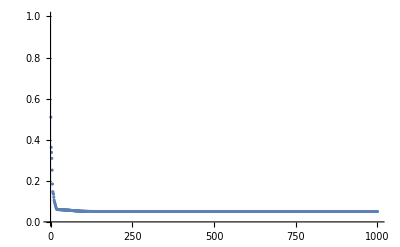

```mathematica
min=Flatten[Position[error[[All,-1]],Min[error[[All,-1]]]]][[1]];ListPlot[error[[min]]/Max[error],PlotRange->{0,1}]
```

```mathematica
inputGSHH=input[[min]];
outputGSHH=output[[min]];
phaseGSHH=phase[[min]];
```

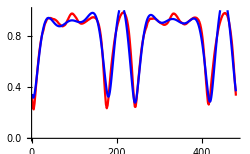
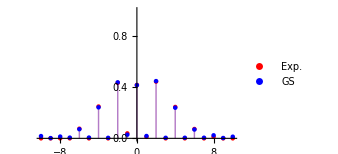

```mathematica
{ListPlot[{Abs[inputbeamHH],Abs[inputGSHH]},PlotRange->{0,1},PlotStyle->{Red,Blue},Joined->True,ImageSize->250],w=10;ListPlot[{RotateRight[Abs[outputbeamHH],(pixels-1)/2][[(pixels+1)/2-w;;(pixels+1)/2+w]],RotateRight[Abs[outputGSHH],(pixels-1)/2][[(pixels+1)/2-w;;(pixels+1)/2+w]]},DataRange->{-w,w},PlotRange->{0,1},PlotStyle->{Red,Blue},Joined->False,Filling->Axis,ImageSize->250,PlotLegends->{"Exp.","GS"}]}
```

### Extracting SU(2) parameters

```mathematica
PhaseGSHH=Table[Mod[phaseGSHH+globalphase[[i]],2N[Pi]],{i,offsets}];
eGSHH=Table[ArcCos[inputbeamHH*Cos[PhaseGSHH[[i]]]],{i,offsets}];
n1GS=Table[-inputbeamHH*Sin[PhaseGSHH[[i]]]/(Sin[eGSHH[[i]]]),{i,offsets}];
```

```mathematica
Manipulate[{ListPlot[PhaseGSHH[[i]],Joined->False,PlotRange->{0,2N[Pi]},PlotStyle->Black,ImageSize->200],ListPlot[eGSHH[[i]],PlotStyle->Red,PlotLegends->Automatic,Joined->True,PlotRange->{0,N[Pi]},ImageSize->200],ListPlot[n1GS[[i]],PlotStyle->Blue,PlotLegends->Automatic,Joined->True,PlotRange->{-1,1},ImageSize->200]},{i,1,offsets,1}]
```

## DD

### Phase retrieval

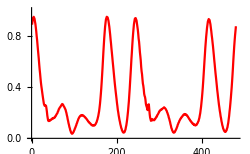
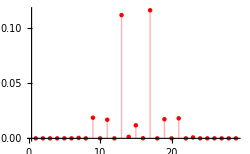

```mathematica
{ListPlot[DDnear,PlotStyle->Red,Joined->True,PlotRange->{0,1},ImageSize->250],ListPlot[DDfar,PlotRange->All,PlotStyle->Red,Joined->False,Filling->Axis,ImageSize->250]}
```

```mathematica
DDfar=ArrayPad[DDfar,(pixels-Length[DDfar])/2](*array-padding needed for implementing the FFT*);
```

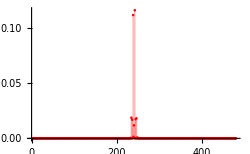
{-Graphics-,-Graphics-}

```mathematica
{ListPlot[DDnear,PlotStyle->Red,Joined->True,PlotRange->{0,1},ImageSize->250],ListPlot[DDfar,PlotRange->All,PlotStyle->Red,Joined->False,Filling->Axis,ImageSize->250]}
```

```mathematica
Dimensions[DDnear]==Dimensions[DDfar]
```

True

```mathematica
inputbeamDD=Sqrt[DDnear](*intensity to amplitude*);
outputbeamDD=RotateLeft[Sqrt[DDfar],(pixels-1)/2](*intensity to amplitude, RotateLeft implements the FFTshift command*);
```

```mathematica
error=Table[{},{i,trials}];
phase=Table[{},{i,trials}];
input=Table[{},{i,trials}];
output=Table[{},{i,trials}];
```

```mathematica
Monitor[
Do[
phaseguess=Table[RandomReal[{0,2N[Pi]}],{i,pixels}];
inputGSguess=inputbeamDD*Exp[I*phaseguess];
InputGS=inputGSguess;
Do[
outputGS=Fourier[InputGS,FourierParameters->{0,1}](*FFT*);
outputGS=outputGS*Sqrt[Total[Abs[outputbeamDD]^2]]/Sqrt[Total[Abs[outputGS]^2]];
phaseoutputGS=Arg[outputGS];
OutputGS=outputbeamDD*Exp[I*phaseoutputGS];
inputGS=Fourier[OutputGS,FourierParameters->{0,-1}](*inverse FFT*);
phaseinputGS=Arg[inputGS];
inputGS=inputGS*Sqrt[Total[Abs[inputbeamDD]^2]]/Sqrt[Total[Abs[inputGS]^2]];
AppendTo[error[[t]],Total[Abs[Abs[inputGS]-inputbeamDD]]];
InputGS=inputbeamDD*Exp[I*phaseinputGS];,
{s,iterations}];
phase[[t]]=phaseinputGS;
input[[t]]=inputGS;
output[[t]]=outputGS;
,{t,trials}],{t,s}]
```

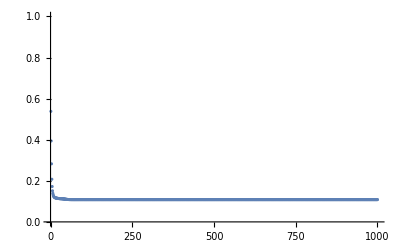

```mathematica
min=Flatten[Position[error[[All,-1]],Min[error[[All,-1]]]]][[1]];ListPlot[error[[min]]/Max[error],PlotRange->{0,1}]
```

```mathematica
inputGSDD=input[[min]];
outputGSDD=output[[min]];
phaseGSDD=phase[[min]];
```

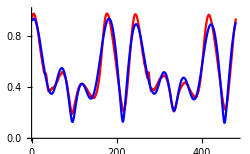
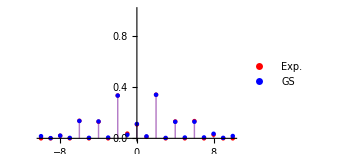

```mathematica
{ListPlot[{Abs[inputbeamDD],Abs[inputGSDD]},PlotRange->{0,1},PlotStyle->{Red,Blue},Joined->True,ImageSize->250],w=10;ListPlot[{RotateRight[Abs[outputbeamDD],(pixels-1)/2][[(pixels+1)/2-w;;(pixels+1)/2+w]],RotateRight[Abs[outputGSDD],(pixels-1)/2][[(pixels+1)/2-w;;(pixels+1)/2+w]]},DataRange->{-w,w},PlotRange->{0,1},PlotStyle->{Red,Blue},Joined->False,Filling->Axis,ImageSize->250,PlotLegends->{"Exp.","GS"}]}
```

### Extracting SU(2) parameters

```mathematica
PhaseGSDD=Table[Mod[phaseGSDD+globalphase[[i]],2N[Pi]],{i,offsets}];
eGSDD=Table[ArcCos[inputbeamDD*Cos[PhaseGSDD[[i]]]],{i,offsets}];
n2GS=Table[-inputbeamDD*Sin[PhaseGSDD[[i]]]/(Sin[eGSDD[[i]]]),{i,offsets}];
```

```mathematica
Manipulate[{ListPlot[PhaseGSDD[[i]],Joined->False,PlotRange->{0,2N[Pi]},PlotStyle->Black,ImageSize->200],ListPlot[eGSDD[[i]],PlotStyle->Red,PlotLegends->Automatic,Joined->True,PlotRange->{0,N[Pi]},ImageSize->200],ListPlot[n2GS[[i]],PlotStyle->Blue,PlotLegends->Automatic,Joined->True,PlotRange->{-1,1},ImageSize->200]},{i,1,offsets,1}]
```

## LL

### Phase retrieval

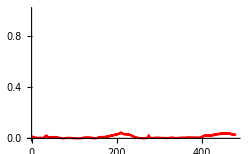
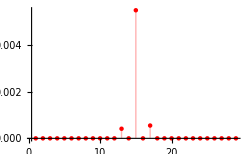

```mathematica
{ListPlot[LLnear,PlotStyle->Red,Joined->True,PlotRange->{0,1},ImageSize->250],ListPlot[LLfar,PlotRange->All,PlotStyle->Red,Joined->False,Filling->Axis,ImageSize->250]}
```

```mathematica
LLfar=ArrayPad[LLfar,(pixels-Length[LLfar])/2](*array-padding needed for implementing the FFT*);
```

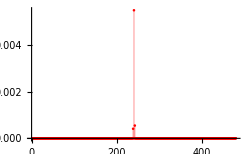
{-Graphics-,-Graphics-}

```mathematica
{ListPlot[LLnear,PlotStyle->Red,Joined->True,PlotRange->{0,1},ImageSize->250],ListPlot[LLfar,PlotRange->All,PlotStyle->Red,Joined->False,Filling->Axis,ImageSize->250]}
```

```mathematica
Dimensions[LLnear]==Dimensions[LLfar]
```

True

```mathematica
inputbeamLL=Sqrt[LLnear](*intensity to amplitude*);
outputbeamLL=RotateLeft[Sqrt[LLfar],(pixels-1)/2](*intensity to amplitude, RotateLeft implements the FFTshift command*);
```

```mathematica
error=Table[{},{i,trials}];
phase=Table[{},{i,trials}];
input=Table[{},{i,trials}];
output=Table[{},{i,trials}];
```

```mathematica
Monitor[
Do[
phaseguess=Table[RandomReal[{0,2N[Pi]}],{i,pixels}];
inputGSguess=inputbeamLL*Exp[I*phaseguess];
InputGS=inputGSguess;
Do[
outputGS=Fourier[InputGS,FourierParameters->{0,1}](*FFT*);
outputGS=outputGS*Sqrt[Total[Abs[outputbeamLL]^2]]/Sqrt[Total[Abs[outputGS]^2]];
phaseoutputGS=Arg[outputGS];
OutputGS=outputbeamLL*Exp[I*phaseoutputGS];
inputGS=Fourier[OutputGS,FourierParameters->{0,-1}](*inverse FFT*);
phaseinputGS=Arg[inputGS];
inputGS=inputGS*Sqrt[Total[Abs[inputbeamLL]^2]]/Sqrt[Total[Abs[inputGS]^2]];
AppendTo[error[[t]],Total[Abs[Abs[inputGS]-inputbeamLL]]];
InputGS=inputbeamLL*Exp[I*phaseinputGS];,
{s,iterations}];
phase[[t]]=phaseinputGS;
input[[t]]=inputGS;
output[[t]]=outputGS;
,{t,trials}],{t,s}]
```

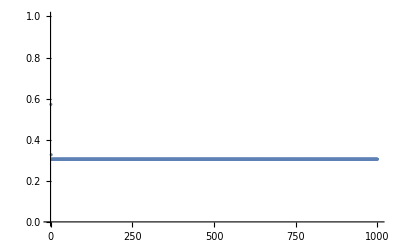

```mathematica
min=Flatten[Position[error[[All,-1]],Min[error[[All,-1]]]]][[1]];ListPlot[error[[min]]/Max[error],PlotRange->{0,1}]
```

```mathematica
inputGSLL=input[[min]];
outputGSLL=output[[min]];
phaseGSLL=phase[[min]];
```

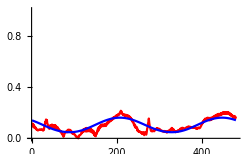
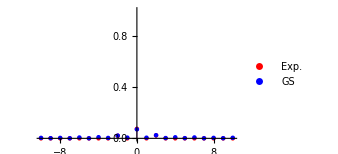

```mathematica
{ListPlot[{Abs[inputbeamLL],Abs[inputGSLL]},PlotRange->{0,1},PlotStyle->{Red,Blue},Joined->True,ImageSize->250],w=10;ListPlot[{RotateRight[Abs[outputbeamLL],(pixels-1)/2][[(pixels+1)/2-w;;(pixels+1)/2+w]],RotateRight[Abs[outputGSLL],(pixels-1)/2][[(pixels+1)/2-w;;(pixels+1)/2+w]]},DataRange->{-w,w},PlotRange->{0,1},PlotStyle->{Red,Blue},Joined->False,Filling->Axis,ImageSize->250,PlotLegends->{"Exp.","GS"}]}
```

### Extracting SU(2) parameters

```mathematica
PhaseGSLL=Table[Mod[phaseGSLL+globalphase[[i]],2N[Pi]],{i,offsets}];
eGSLL=Table[ArcCos[inputbeamLL*Cos[PhaseGSLL[[i]]]],{i,offsets}];
n3GS=Table[-inputbeamLL*Sin[PhaseGSLL[[i]]]/(Sin[eGSLL[[i]]]),{i,offsets}];
```

```mathematica
Manipulate[{ListPlot[PhaseGSLL[[i]],Joined->False,PlotRange->{0,2N[Pi]},PlotStyle->Black,ImageSize->200],ListPlot[eGSLL[[i]],PlotStyle->Red,PlotLegends->Automatic,Joined->True,PlotRange->{0,N[Pi]},ImageSize->200],ListPlot[n3GS[[i]],PlotStyle->Blue,PlotLegends->Automatic,Joined->True,PlotRange->{-1,1},ImageSize->200]},{i,1,offsets,1}]
```

## Matching the global phase

```mathematica
ΔHD=Table[Total[(eGSHH[[i]]-eGSDD[[j]])^2],{i,offsets},{j,offsets}];
ΔHL=Table[Total[(eGSHH[[i]]-eGSLL[[j]])^2],{i,offsets},{j,offsets}];
```

```mathematica
posminHD=Table[Position[ΔHD[[i]],Min[ΔHD[[i]]]][[1,1]],{i,offsets}];
```

```mathematica
posminHL=Table[Position[ΔHL[[i]],Min[ΔHL[[i]]]][[1,1]],{i,offsets}];
```

```mathematica
n=Table[{n1GS[[i]],n2GS[[posminHD[[i]]]],n3GS[[posminHL[[i]]]]},{i,offsets}];
```

```mathematica
n1=Table[n[[i,1,x]],{i,offsets},{x,pixels}];
n2=Table[n[[i,2,x]],{i,offsets},{x,pixels}];
n3=Table[n[[i,3,x]],{i,offsets},{x,pixels}];
```

```mathematica
norm=Table[n1[[i]]^2+n2[[i]]^2+n3[[i]]^2,{i,offsets}];
```

```mathematica
n1=Table[n1[[i]]/Sqrt[norm[[i]]],{i,offsets}];
n2=Table[n2[[i]]/Sqrt[norm[[i]]],{i,offsets}];
n3=Table[n3[[i]]/Sqrt[norm[[i]]],{i,offsets}];
```

```mathematica
possibleU=Table[Cos[eGSHH[[i,x]]]*IdentityMatrix[2]-I Sin[eGSHH[[i,x]]](n1[[i,x]]*PauliMatrix[1]+n2[[i,x]]*PauliMatrix[2]+n3[[i,x]]*PauliMatrix[3]),{i,offsets},{x,pixels}];
```

## Finding the unitary

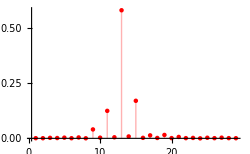

```mathematica
ListPlot[probtot,PlotRange->All,PlotStyle->Red,Joined->False,Filling->Axis,ImageSize->250]
```

```mathematica
probtot=ArrayPad[probtot,(pixels-Length[probtot])/2](*array-padding needed for implementing the FFT*);
```

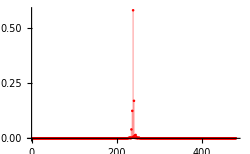

```mathematica
ListPlot[probtot,PlotRange->All,PlotStyle->Red,Joined->False,Filling->Axis,ImageSize->250]
```

```mathematica
outputbeamtot=RotateLeft[probtot,(pixels-1)/2](*experimental measurement*);
```

```mathematica
state={1,0}(*left-circular input polarization*);
```

```mathematica
transfbeam=Table[possibleU[[i,x]].state,{i,offsets},{x,pixels}];
```

```mathematica
transfbeam1=Table[transfbeam[[i,x,1]],{i,offsets},{x,pixels}];
transfbeam2=Table[transfbeam[[i,x,2]],{i,offsets},{x,pixels}];
outputtot1=Table[Fourier[transfbeam1[[i]],FourierParameters->{0,1}],{i,offsets}];
outputtot2=Table[Fourier[transfbeam2[[i]],FourierParameters->{0,1}],{i,offsets}];
(*each spinor component must be Fourier-transformed individually*)
```

```mathematica
outputtot=Table[{outputtot1[[i,x]],outputtot2[[i,x]]},{i,offsets},{x,pixels}];
(*recombine the Fourier-transformed spinor*)
```

```mathematica
outputpower=Table[Norm[outputtot[[i,x]]]^2,{i,offsets},{x,pixels}];
outputpower=Table[outputpower[[i]]/Total[outputpower[[i]]],{i,offsets}](*normalize far-field intensity*);
```

```mathematica
Manipulate[w=10;ListPlot[{RotateRight[outputbeamtot,(pixels-1)/2][[(pixels+1)/2-w;;(pixels+1)/2+w]],RotateRight[outputpower[[i]],(pixels-1)/2][[(pixels+1)/2-w;;(pixels+1)/2+w]]},DataRange->{-w,w},PlotRange->{0,1},Filling->Axis,PlotStyle->{Red,Blue}],{i,1,offsets,1}]
```

```mathematica
dist=Table[{Total[(outputpower[[i]]-outputbeamtot)^2],i},{i,offsets}];
min=SortBy[dist,First][[1,2]];
```

## Reconstructed parameters

```mathematica
efqpt=eGSHH[[min]];
n1fqpt=n1[[min]];
n2fqpt=n2[[min]];
n3fqpt=n3[[min]];
```

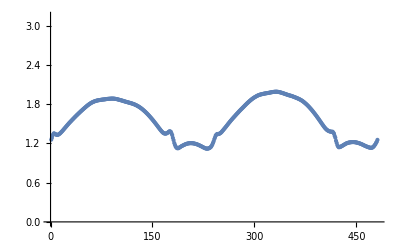
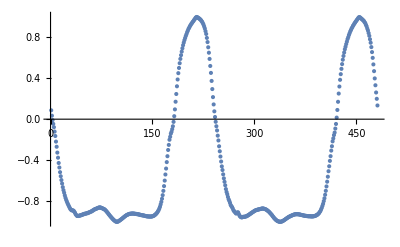
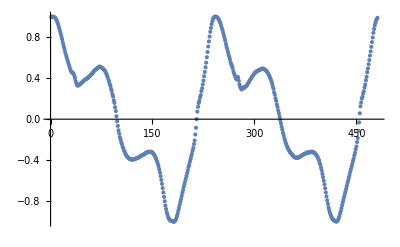
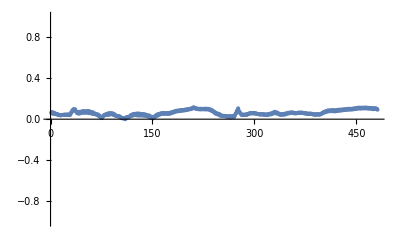

```mathematica
{ListPlot[efqpt,PlotRange->{0,N[Pi]}],ListPlot[n1fqpt,PlotRange->{-1,1}],ListPlot[n2fqpt,PlotRange->{-1,1}],ListPlot[n3fqpt,PlotRange->{-1,1}]}
```

## 2D Fourier Quantum Process Tomography

### Experimental parameters

```mathematica
pixelsize=5.2*10^-6(*in meters*);
Λ=2.5*10^-3(*spatial period, in meters*);
```

```mathematica
pixels=Round[Λ/pixelsize](*how many pixels in a period*)
```

481

```mathematica
integrationpixels=11(*integration window to compress the images*);
```

```mathematica
pixels=Floor[pixels/integrationpixels](*effective pixels after integration*)
```

43

### Algorithm parameters

```mathematica
offsets=64;
globalphase=Subdivide[0,2N[Pi],offsets-1](*global offsets for reconstructed phases*);
trials=50(*how many independent executions of the GS algorithm*);
iterations=500(*how many iterations within a single execution*);
```

## Import experimental data

```mathematica
SetDirectory[NotebookDirectory[]<>"\\Data\\2D"]
```

C:\Users\franc\Desktop\postdoc\research\QPT_GS\github\Data\2D

```mathematica
HHnear=Import["HH_near.txt","Table"];
HHfar=Import["HH_far.txt","Table"];
```

```mathematica
DDnear=Import["DD_near.txt","Table"];
DDfar=Import["DD_far.txt","Table"];
```

```mathematica
LLnear=Import["LL_near.txt","Table"];
LLfar=Import["LL_far.txt","Table"];
```

```mathematica
probtot=Import["far_total.txt","Table"];
```

## HH

### Phase retrieval

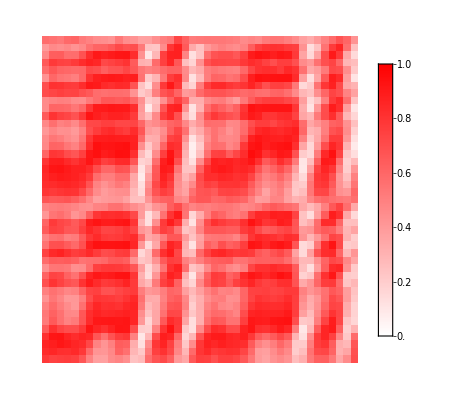
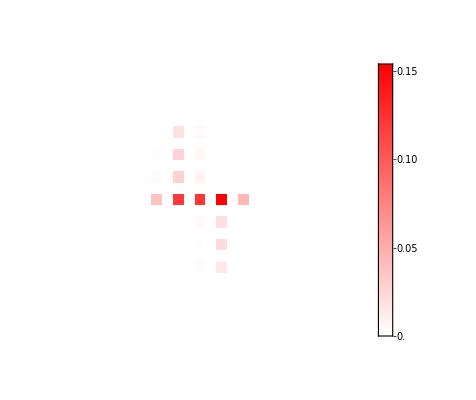

```mathematica
{ArrayPlot[HHnear,ColorFunction->(Blend[{White,Red},#]&),PlotRange->{0,1},PlotLegends->Automatic],ArrayPlot[HHfar,ColorFunction->(Blend[{White,Red},#]&),PlotRange->All,PlotLegends->Automatic]}
```

```mathematica
HHfar=ArrayPad[HHfar,(pixels-Length[HHfar])/2](*array-padding needed for implementing the FFT*);
```

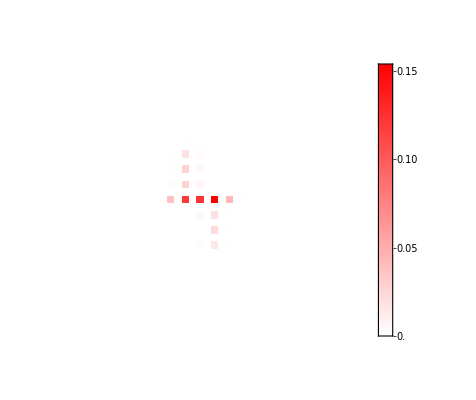
{-Graphics-,-Graphics-}

```mathematica
{ArrayPlot[HHnear,ColorFunction->(Blend[{White,Red},#]&),PlotRange->{0,1},PlotLegends->Automatic],ArrayPlot[HHfar,ColorFunction->(Blend[{White,Red},#]&),PlotRange->All,PlotLegends->Automatic]}
```

```mathematica
Dimensions[HHnear]==Dimensions[HHfar]
```

True

```mathematica
inputbeamHH=Sqrt[HHnear](*intensity to amplitude*);
outputbeamHH=RotateLeft[Sqrt[HHfar],{(pixels-1)/2,(pixels-1)/2}](*intensity to amplitude, RotateLeft implements the FFTshift command*);
```

```mathematica
error=Table[{},{i,trials}];
phase=Table[{},{i,trials}];
input=Table[{},{i,trials}];
output=Table[{},{i,trials}];
```

```mathematica
Monitor[
Do[
phaseguess=Table[RandomReal[{0,2N[Pi]}],{i,pixels},{j,pixels}];
inputGSguess=inputbeamHH*Exp[I*phaseguess];
InputGS=inputGSguess;
Do[
outputGS=Fourier[InputGS,FourierParameters->{0,1}](*FFT*);
outputGS=outputGS*Sqrt[Total[Abs[outputbeamHH]^2,2]]/Sqrt[Total[Abs[outputGS]^2,2]];
phaseoutputGS=Arg[outputGS];
OutputGS=outputbeamHH*Exp[I*phaseoutputGS];
inputGS=Fourier[OutputGS,FourierParameters->{0,-1}](*inverse FFT*);
phaseinputGS=Arg[inputGS];
inputGS=inputGS*Sqrt[Total[Abs[inputbeamHH]^2,2]]/Sqrt[Total[Abs[inputGS]^2,2]];
AppendTo[error[[t]],Total[Abs[Abs[inputGS]-inputbeamHH],2]];
InputGS=inputbeamHH*Exp[I*phaseinputGS];,
{s,iterations}];
phase[[t]]=phaseinputGS;
input[[t]]=inputGS;
output[[t]]=outputGS;
,{t,trials}],{t,s}]
```

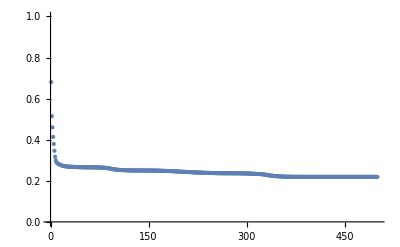

```mathematica
min=Flatten[Position[error[[All,-1]],Min[error[[All,-1]]]]][[1]];ListPlot[error[[min]]/Max[error],PlotRange->{0,1}]
```

```mathematica
inputGSHH=input[[min]];
outputGSHH=output[[min]];
phaseGSHH=phase[[min]];
```

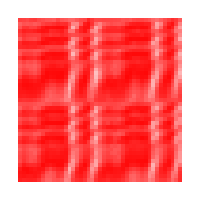
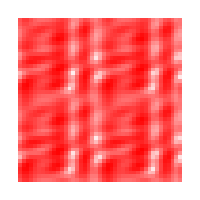

```mathematica
{ArrayPlot[Abs[inputbeamHH],ColorFunction->(Blend[{White,Red},#]&),PlotRange->{0,1},ImageSize->200],ArrayPlot[Abs[inputGSHH],ColorFunction->(Blend[{White,Red},#]&),PlotRange->{0,Max[Abs[inputGSHH]]},ImageSize->200]}
```

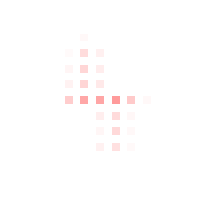
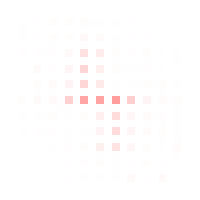

```mathematica
{w=10;ArrayPlot[RotateRight[Abs[outputbeamHH],{(pixels-1)/2,(pixels-1)/2}][[(pixels+1)/2-w;;(pixels+1)/2+w,(pixels+1)/2-w;;(pixels+1)/2+w]],ColorFunction->(Blend[{White,Red},#]&),PlotRange->{0,1},ImageSize->200],ArrayPlot[RotateRight[Abs[outputGSHH],{(pixels-1)/2,(pixels-1)/2}][[(pixels+1)/2-w;;(pixels+1)/2+w,(pixels+1)/2-w;;(pixels+1)/2+w]],ColorFunction->(Blend[{White,Red},#]&),PlotRange->{0,1},ImageSize->200]}
```

### Extracting SU(2) parameters

```mathematica
PhaseGSHH=Table[Mod[phaseGSHH+globalphase[[i]],2N[Pi]],{i,offsets}];
eGSHH=Table[ArcCos[inputbeamHH*Cos[PhaseGSHH[[i]]]],{i,offsets}];
n1GS=Table[-inputbeamHH*Sin[PhaseGSHH[[i]]]/(Sin[eGSHH[[i]]]),{i,offsets}];
```

```mathematica
Manipulate[{ArrayPlot[PhaseGSHH[[i]],ColorFunction->Hue,PlotRange->{0,2N[Pi]},ImageSize->200],ArrayPlot[eGSHH[[i]],ColorFunction->"Rainbow",PlotRange->{0,N[Pi]},ImageSize->200],ArrayPlot[n1GS[[i]],ColorFunction->"Rainbow",PlotRange->{-1,1},ImageSize->200]},{i,1,offsets,1}]
```

## DD

### Phase retrieval

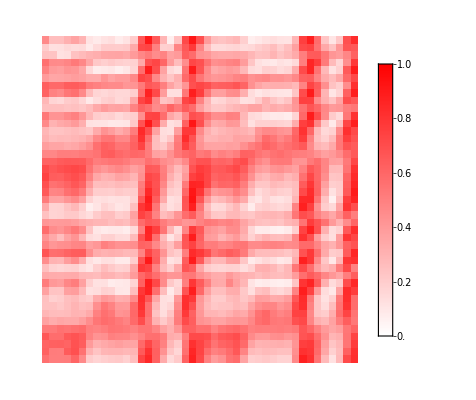
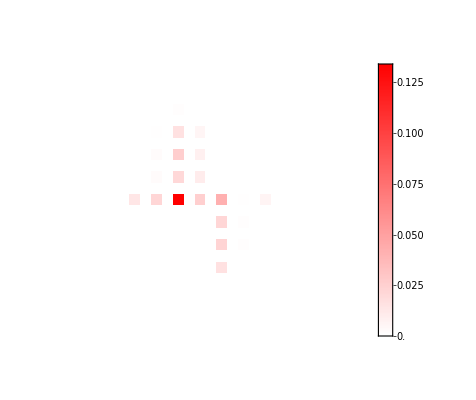

```mathematica
{ArrayPlot[DDnear,ColorFunction->(Blend[{White,Red},#]&),PlotRange->{0,1},PlotLegends->Automatic],ArrayPlot[DDfar,ColorFunction->(Blend[{White,Red},#]&),PlotRange->All,PlotLegends->Automatic]}
```

```mathematica
DDfar=ArrayPad[DDfar,(pixels-Length[DDfar])/2](*array-padding needed for implementing the FFT*);
```

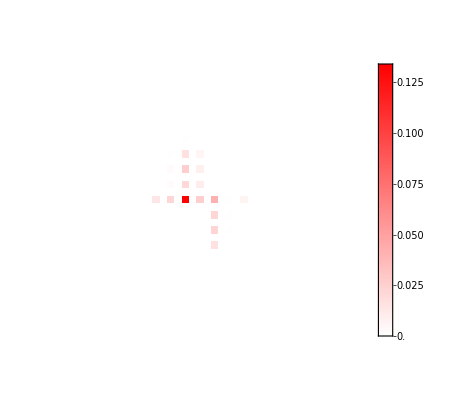
{-Graphics-,-Graphics-}

```mathematica
{ArrayPlot[DDnear,ColorFunction->(Blend[{White,Red},#]&),PlotRange->{0,1},PlotLegends->Automatic],ArrayPlot[DDfar,ColorFunction->(Blend[{White,Red},#]&),PlotRange->All,PlotLegends->Automatic]}
```

```mathematica
Dimensions[DDnear]==Dimensions[DDfar]
```

True

```mathematica
inputbeamDD=Sqrt[DDnear](*intensity to amplitude*);
outputbeamDD=RotateLeft[Sqrt[DDfar],{(pixels-1)/2,(pixels-1)/2}](*intensity to amplitude, RotateLeft implements the FFTshift command*);
```

```mathematica
error=Table[{},{i,trials}];
phase=Table[{},{i,trials}];
input=Table[{},{i,trials}];
output=Table[{},{i,trials}];
```

```mathematica
Monitor[
Do[
phaseguess=Table[RandomReal[{0,2N[Pi]}],{i,pixels},{j,pixels}];
inputGSguess=inputbeamDD*Exp[I*phaseguess];
InputGS=inputGSguess;
Do[
outputGS=Fourier[InputGS,FourierParameters->{0,1}](*FFT*);
outputGS=outputGS*Sqrt[Total[Abs[outputbeamDD]^2,2]]/Sqrt[Total[Abs[outputGS]^2,2]];
phaseoutputGS=Arg[outputGS];
OutputGS=outputbeamDD*Exp[I*phaseoutputGS];
inputGS=Fourier[OutputGS,FourierParameters->{0,-1}](*inverse FFT*);
phaseinputGS=Arg[inputGS];
inputGS=inputGS*Sqrt[Total[Abs[inputbeamDD]^2,2]]/Sqrt[Total[Abs[inputGS]^2,2]];
AppendTo[error[[t]],Total[Abs[Abs[inputGS]-inputbeamDD],2]];
InputGS=inputbeamDD*Exp[I*phaseinputGS];,
{s,iterations}];
phase[[t]]=phaseinputGS;
input[[t]]=inputGS;
output[[t]]=outputGS;
,{t,trials}],{t,s}]
```

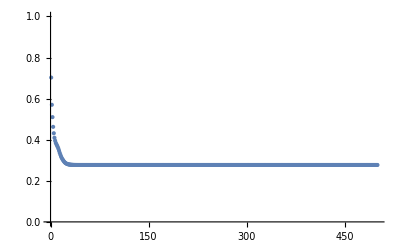

```mathematica
min=Flatten[Position[error[[All,-1]],Min[error[[All,-1]]]]][[1]];ListPlot[error[[min]]/Max[error],PlotRange->{0,1}]
```

```mathematica
inputGSDD=input[[min]];
outputGSDD=output[[min]];
phaseGSDD=phase[[min]];
```

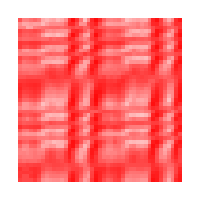
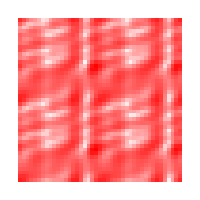

```mathematica
{ArrayPlot[Abs[inputbeamDD],ColorFunction->(Blend[{White,Red},#]&),PlotRange->{0,1},ImageSize->200],ArrayPlot[Abs[inputGSDD],ColorFunction->(Blend[{White,Red},#]&),PlotRange->{0,Max[Abs[inputGSDD]]},ImageSize->200]}
```

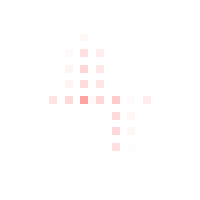
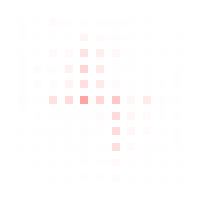

```mathematica
{w=10;ArrayPlot[RotateRight[Abs[outputbeamDD],{(pixels-1)/2,(pixels-1)/2}][[(pixels+1)/2-w;;(pixels+1)/2+w,(pixels+1)/2-w;;(pixels+1)/2+w]],ColorFunction->(Blend[{White,Red},#]&),PlotRange->{0,1},ImageSize->200],ArrayPlot[RotateRight[Abs[outputGSDD],{(pixels-1)/2,(pixels-1)/2}][[(pixels+1)/2-w;;(pixels+1)/2+w,(pixels+1)/2-w;;(pixels+1)/2+w]],ColorFunction->(Blend[{White,Red},#]&),PlotRange->{0,1},ImageSize->200]}
```

### Extracting SU(2) parameters

```mathematica
PhaseGSDD=Table[Mod[phaseGSDD+globalphase[[i]],2N[Pi]],{i,offsets}];
eGSDD=Table[ArcCos[inputbeamDD*Cos[PhaseGSDD[[i]]]],{i,offsets}];
n2GS=Table[-inputbeamDD*Sin[PhaseGSDD[[i]]]/(Sin[eGSDD[[i]]]),{i,offsets}];
```

```mathematica
Manipulate[{ArrayPlot[PhaseGSDD[[i]],ColorFunction->Hue,PlotRange->{0,2N[Pi]},ImageSize->200],ArrayPlot[eGSDD[[i]],ColorFunction->"Rainbow",PlotRange->{0,N[Pi]},ImageSize->200],ArrayPlot[n2GS[[i]],ColorFunction->"Rainbow",PlotRange->{-1,1},ImageSize->200]},{i,1,offsets,1}]
```

## LL

### Phase retrieval

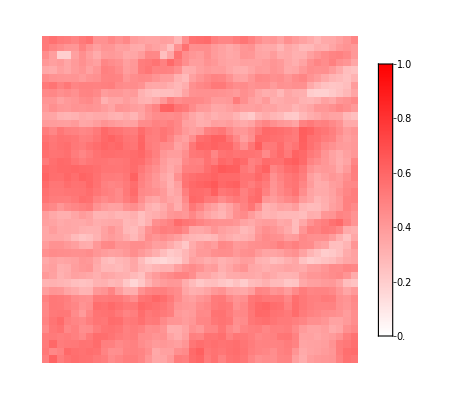
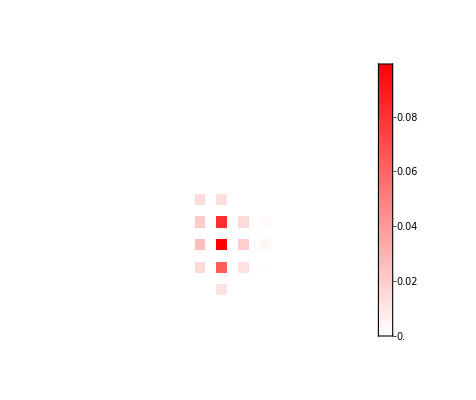

```mathematica
{ArrayPlot[LLnear,ColorFunction->(Blend[{White,Red},#]&),PlotRange->{0,1},PlotLegends->Automatic],ArrayPlot[LLfar,ColorFunction->(Blend[{White,Red},#]&),PlotRange->All,PlotLegends->Automatic]}
```

```mathematica
LLfar=ArrayPad[LLfar,(pixels-Length[LLfar])/2](*array-padding needed for implementing the FFT*);
```

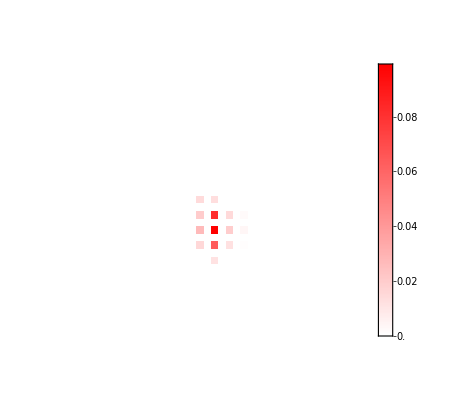
{-Graphics-,-Graphics-}

```mathematica
{ArrayPlot[LLnear,ColorFunction->(Blend[{White,Red},#]&),PlotRange->{0,1},PlotLegends->Automatic],ArrayPlot[LLfar,ColorFunction->(Blend[{White,Red},#]&),PlotRange->All,PlotLegends->Automatic]}
```

```mathematica
Dimensions[LLnear]==Dimensions[LLfar]
```

True

```mathematica
inputbeamLL=Sqrt[LLnear](*intensity to amplitude*);
outputbeamLL=RotateLeft[Sqrt[LLfar],{(pixels-1)/2,(pixels-1)/2}](*intensity to amplitude, RotateLeft implements the FFTshift command*);
```

```mathematica
error=Table[{},{i,trials}];
phase=Table[{},{i,trials}];
input=Table[{},{i,trials}];
output=Table[{},{i,trials}];
```

```mathematica
Monitor[
Do[
phaseguess=Table[RandomReal[{0,2N[Pi]}],{i,pixels},{j,pixels}];
inputGSguess=inputbeamLL*Exp[I*phaseguess];
InputGS=inputGSguess;
Do[
outputGS=Fourier[InputGS,FourierParameters->{0,1}](*FFT*);
outputGS=outputGS*Sqrt[Total[Abs[outputbeamLL]^2,2]]/Sqrt[Total[Abs[outputGS]^2,2]];
phaseoutputGS=Arg[outputGS];
OutputGS=outputbeamLL*Exp[I*phaseoutputGS];
inputGS=Fourier[OutputGS,FourierParameters->{0,-1}](*inverse FFT*);
phaseinputGS=Arg[inputGS];
inputGS=inputGS*Sqrt[Total[Abs[inputbeamLL]^2,2]]/Sqrt[Total[Abs[inputGS]^2,2]];
AppendTo[error[[t]],Total[Abs[Abs[inputGS]-inputbeamLL],2]];
InputGS=inputbeamLL*Exp[I*phaseinputGS];,
{s,iterations}];
phase[[t]]=phaseinputGS;
input[[t]]=inputGS;
output[[t]]=outputGS;
,{t,trials}],{t,s}]
```

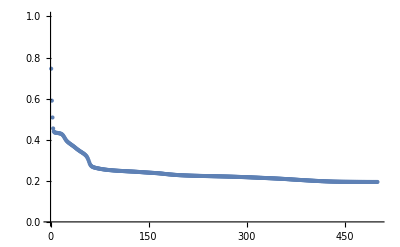

```mathematica
min=Flatten[Position[error[[All,-1]],Min[error[[All,-1]]]]][[1]];ListPlot[error[[min]]/Max[error],PlotRange->{0,1}]
```

```mathematica
inputGSLL=input[[min]];
outputGSLL=output[[min]];
phaseGSLL=phase[[min]];
```

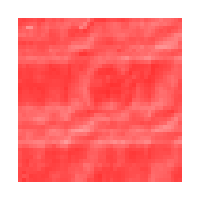
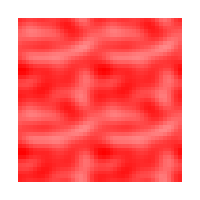

```mathematica
{ArrayPlot[Abs[inputbeamLL],ColorFunction->(Blend[{White,Red},#]&),PlotRange->{0,1},ImageSize->200],ArrayPlot[Abs[inputGSLL],ColorFunction->(Blend[{White,Red},#]&),PlotRange->{0,Max[Abs[inputGSLL]]},ImageSize->200]}
```

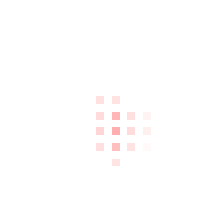
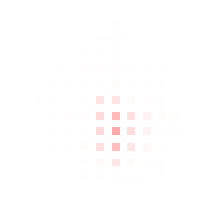

```mathematica
{w=10;ArrayPlot[RotateRight[Abs[outputbeamLL],{(pixels-1)/2,(pixels-1)/2}][[(pixels+1)/2-w;;(pixels+1)/2+w,(pixels+1)/2-w;;(pixels+1)/2+w]],ColorFunction->(Blend[{White,Red},#]&),PlotRange->{0,1},ImageSize->200],ArrayPlot[RotateRight[Abs[outputGSLL],{(pixels-1)/2,(pixels-1)/2}][[(pixels+1)/2-w;;(pixels+1)/2+w,(pixels+1)/2-w;;(pixels+1)/2+w]],ColorFunction->(Blend[{White,Red},#]&),PlotRange->{0,1},ImageSize->200]}
```

### Extracting SU(2) parameters

```mathematica
PhaseGSLL=Table[Mod[phaseGSLL+globalphase[[i]],2N[Pi]],{i,offsets}];
eGSLL=Table[ArcCos[inputbeamLL*Cos[PhaseGSLL[[i]]]],{i,offsets}];
n3GS=Table[-inputbeamLL*Sin[PhaseGSLL[[i]]]/(Sin[eGSLL[[i]]]),{i,offsets}];
```

```mathematica
Manipulate[{ArrayPlot[PhaseGSLL[[i]],ColorFunction->Hue,PlotRange->{0,2N[Pi]},ImageSize->200],ArrayPlot[eGSLL[[i]],ColorFunction->"Rainbow",PlotRange->{0,N[Pi]},ImageSize->200],ArrayPlot[n3GS[[i]],ColorFunction->"Rainbow",PlotRange->{-1,1},ImageSize->200]},{i,1,offsets,1}]
```

## Matching the global phase

```mathematica
ΔHD=Table[Total[(eGSHH[[i]]-eGSDD[[j]])^2,2],{i,offsets},{j,offsets}];
ΔHL=Table[Total[(eGSHH[[i]]-eGSLL[[j]])^2,2],{i,offsets},{j,offsets}];
```

```mathematica
posminHD=Table[Position[ΔHD[[i]],Min[ΔHD[[i]]]][[1,1]],{i,offsets}];
```

```mathematica
posminHL=Table[Position[ΔHL[[i]],Min[ΔHL[[i]]]][[1,1]],{i,offsets}];
```

```mathematica
n=Table[{n1GS[[i]],n2GS[[posminHD[[i]]]],n3GS[[posminHL[[i]]]]},{i,offsets}];
```

```mathematica
n1=Table[n[[i,1,x,y]],{i,offsets},{x,pixels},{y,pixels}];
n2=Table[n[[i,2,x,y]],{i,offsets},{x,pixels},{y,pixels}];
n3=Table[n[[i,3,x,y]],{i,offsets},{x,pixels},{y,pixels}];
```

```mathematica
norm=Table[n1[[i]]^2+n2[[i]]^2+n3[[i]]^2,{i,offsets}];
```

```mathematica
n1=Table[n1[[i]]/Sqrt[norm[[i]]],{i,offsets}];
n2=Table[n2[[i]]/Sqrt[norm[[i]]],{i,offsets}];
n3=Table[n3[[i]]/Sqrt[norm[[i]]],{i,offsets}];
```

```mathematica
possibleU=Table[Cos[eGSHH[[i,x,y]]]*IdentityMatrix[2]-I Sin[eGSHH[[i,x,y]]](n1[[i,x,y]]*PauliMatrix[1]+n2[[i,x,y]]*PauliMatrix[2]+n3[[i,x,y]]*PauliMatrix[3]),{i,offsets},{x,pixels},{y,pixels}];
```

## Finding the unitary

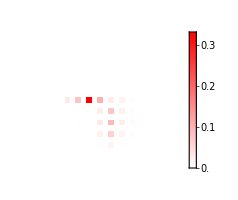

```mathematica
ArrayPlot[probtot,ColorFunction->(Blend[{White,Red},#]&),PlotRange->All,PlotLegends->Automatic,ImageSize->200]
```

```mathematica
probtot=ArrayPad[probtot,{(pixels-Length[probtot])/2,(pixels-Length[probtot])/2}](*array-padding needed for implementing the FFT*);
```

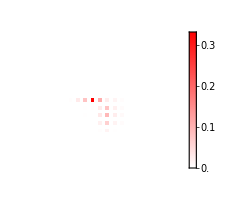

```mathematica
ArrayPlot[probtot,ColorFunction->(Blend[{White,Red},#]&),PlotRange->All,PlotLegends->Automatic,ImageSize->200]
```

```mathematica
outputbeamtot=RotateLeft[probtot,{(pixels-1)/2,(pixels-1)/2}](*experimental measurement*);
```

```mathematica
state={1,0}(*left-circular input polarization*);
```

```mathematica
transfbeam=Table[possibleU[[i,x,y]].state,{i,offsets},{x,pixels},{y,pixels}];
```

```mathematica
transfbeam1=Table[transfbeam[[i,x,y,1]],{i,offsets},{x,pixels},{y,pixels}];
transfbeam2=Table[transfbeam[[i,x,y,2]],{i,offsets},{x,pixels},{y,pixels}];
outputtot1=Table[Fourier[transfbeam1[[i]],FourierParameters->{0,1}],{i,offsets}];
outputtot2=Table[Fourier[transfbeam2[[i]],FourierParameters->{0,1}],{i,offsets}];
(*each spinor component must be Fourier-transformed individually*)
```

```mathematica
outputtot=Table[{outputtot1[[i,x,y]],outputtot2[[i,x,y]]},{i,offsets},{x,pixels},{y,pixels}];
(*recombine the Fourier-transformed spinor*)
```

```mathematica
outputpower=Table[Norm[outputtot[[i,x,y]]]^2,{i,offsets},{x,pixels},{y,pixels}];
outputpower=Table[outputpower[[i]]/Total[outputpower[[i]],2],{i,offsets}](*normalize far-field intensity*);
```

```mathematica
Manipulate[w=10;{ArrayPlot[RotateRight[outputbeamtot,{(pixels-1)/2,(pixels-1)/2}][[(pixels+1)/2-w;;(pixels+1)/2+w,(pixels+1)/2-w;;(pixels+1)/2+w]],ColorFunction->(Blend[{White,Red},#]&),PlotRange->{0,1}],ArrayPlot[RotateRight[outputpower[[i]],{(pixels-1)/2,(pixels-1)/2}][[(pixels+1)/2-w;;(pixels+1)/2+w,(pixels+1)/2-w;;(pixels+1)/2+w]],ColorFunction->(Blend[{White,Red},#]&),PlotRange->{0,1}]},{i,1,offsets,1}]
```

```mathematica
dist=Table[{Total[(outputpower[[i]]-outputbeamtot)^2,2],i},{i,offsets}];
min=SortBy[dist,First][[1,2]];
```

## Reconstructed parameters

```mathematica
efqpt=eGSHH[[min]];
n1fqpt=n1[[min]];
n2fqpt=n2[[min]];
n3fqpt=n3[[min]];
```

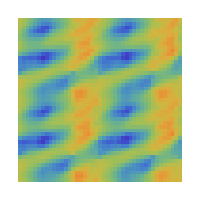
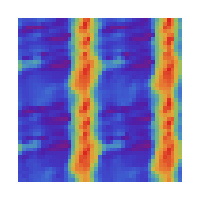
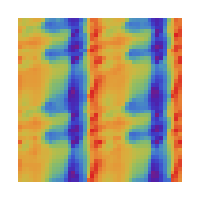
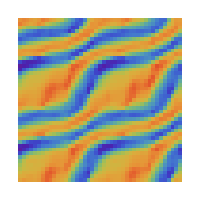

```mathematica
{ArrayPlot[efqpt,ColorFunction->"Rainbow",PlotRange->{0,N[Pi]},ImageSize->200],ArrayPlot[n1fqpt,ColorFunction->"Rainbow",PlotRange->{-1,1},ImageSize->200],ArrayPlot[n2fqpt,ColorFunction->"Rainbow",PlotRange->{-1,1},ImageSize->200],ArrayPlot[n3fqpt,ColorFunction->"Rainbow",PlotRange->{-1,1},ImageSize->200]}
```